```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY187/sec_int_data/500nm.dat"]
```

{{1.45287,0.28983},{1.39708,0.251848},{1.35876,0.226817},{1.32403,0.215434},{1.28662,0.212447},{1.25869,0.205875},{1.22636,0.207664},{1.19613,0.218975},{1.17366,0.210747},{1.15413,0.196471},{1.12528,0.180904},{1.11495,0.215353},{1.10625,0.224023},{1.09912,0.23752},{1.09306,0.255417},{1.0888,0.268881},{1.08648,0.256037},{1.08572,0.243652},{1.08632,0.196882},{1.0888,0.189049},{1.09505,0.239253},{1.09559,0.25441},{1.12528,0.291475},{1.14263,0.316197},{1.16354,0.334756},{1.19414,0.343164},{1.22405,0.346281},{1.25343,0.35347},{1.28081,0.341744},{1.31748,0.339183},{1.36987,0.3354},{1.42194,0.326061},{1.47153,0.300697},{1.11308,0.29431}}

0.0729519+0.156796 x

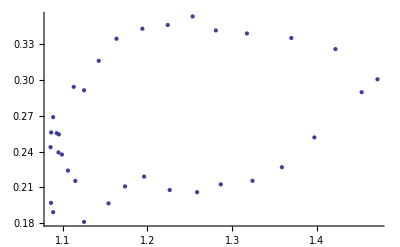

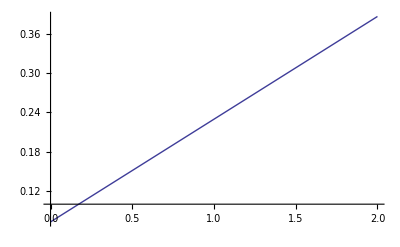

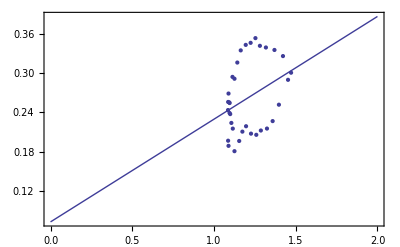

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```